# Linear Sigma model (LSM)

```mathematica
NotebookDirectory[]
```

/home/raj/C_SM/ToySMat1Loop/

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$model="LSM";
```

```mathematica
<<GenAmp`
```

Patched 2 FeynArts models.

## Setup

```mathematica
$gaugerules=Join[M$IntParams,{FAGaugeXi[S[1]]:> 1}];
```

```mathematica
$ampconfigFCFAConvert={ChangeDimension->D,Contract->False,DropSumOver->False,FCFADiracChainJoin->True,FeynAmpDenominatorCombine->True,
FinalSubstitutions->{},InitialSubstitutions->{},List->False,LoopMomenta->{l},LorentzIndexNames->{},Prefactor->1,SMP->False,SUNFIndexNames->{},
SUNIndexNames->{},TransversePolarizationVectors->{},UndoChiralSplittings->False};
```

## Tadpole (1->0)

## One Loop H->0

loading generic model file /home/raj/C_SM/ToySMat1Loop/models/LSM/LSM.gen

> $GenericMixing is OFF

generic model {./models/LSM/LSM} initialized

loading classes model file /home/raj/C_SM/ToySMat1Loop/models/LSM/LSM.mod

> 2 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 5 vertices

> 8 counterterms of order 1

classes model {./models/LSM/LSM} initialized

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

in total: 2 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ab/0/bb.m, 0 diagrams

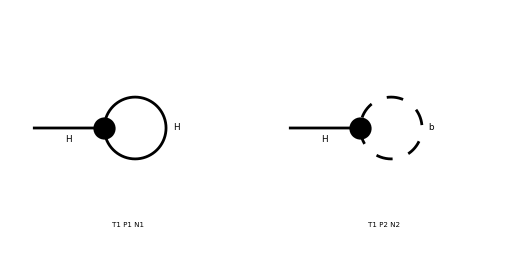

> Top. 1 ab/0/0.m, 0 diagrams

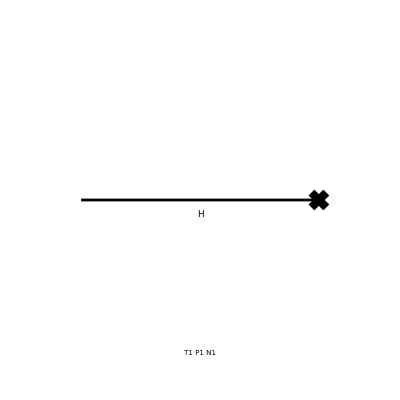

```mathematica
D1LH=diag[1,{S[1]},{}];
```

```mathematica
Amp1LH=D1LH//amp1L[{p1},{}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

Part::partw: Part 2 of {} does not exist.

{-(ⅈ g4 vev)/(64 π^4 l^2)-(3 ⅈ g4 vev)/(64 π^4 (l^2-(g4 vev^2)/2)),-1/4 g4 vev^3 √ZH (Zv-1) Zv (Zv+1)}

```mathematica
Amp1LHDiv=Amp1LH//amp1LSimplify[{Zv:> 1+Nd dv,ZH:> 1+Nd dH},{SMP["Delta"],dv,dH}]
```

(3 Δ g4^2 vev^3)/(64 π^2)-1/2 dv g4 vev^3

```mathematica
dsol[1]=Solve[SelectFree2[Amp1LHDiv,p1]==0,dv]//Flatten//Simplify
dSave[dsol[1]];
```

{dv→(3 Δ g4)/(32 π^2)}

## One Loop (1->1)

## One Loop S->S

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 2 Particles insertions

in total: 4 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

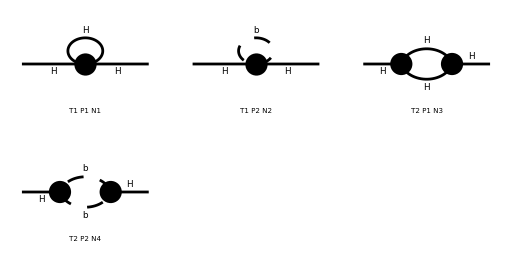

> Top. 1 ac/bc/0.m, 0 diagrams

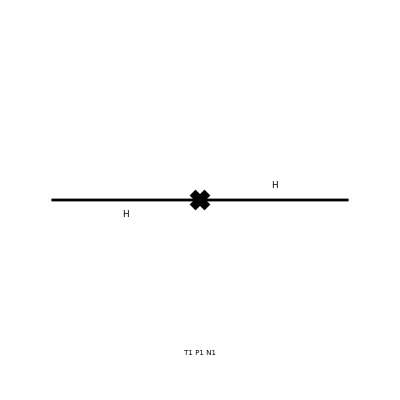

```mathematica
D1LHH=diag[1,{S[1]},{S[1]}];
```

```mathematica
Amp1LHH=D1LHH//amp1L[{p1},{p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

in total: 4 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(9 ⅈ g4^2 vev^2)/(128 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2-(g4 vev^2)/2))-(3 ⅈ g4)/(64 π^4 (l^2-(g4 vev^2)/2))+-(ⅈ g4^2 vev^2)/(128 π^4 l^2.(l-p1)^2)-(ⅈ g4)/(64 π^4 l^2),-ⅈ (ⅈ p1^2 (ZH-1)-1/4 ⅈ g4 vev^2 (2 ZH ZmH^2 Zv^2+ZH Zv^2-ZH-2))}

```mathematica
Amp1LHHDiv=Amp1LHH//amp1LSimplify[{ZH:> 1+Nd dH,ZmH:> 1+Nd dmH,Zv:> 1+Nd dv},{SMP["Delta"],dH, dmH,dv}]
```

-1/2 dH g4 vev^2+dH p1^2-dmH g4 vev^2-3/2 dv g4 vev^2+(13 Δ g4^2 vev^2)/(64 π^2)

```mathematica
dsol[2]=Solve[SelectNotFree2[Amp1LHHDiv/.dSub[dH],p1]==0,dH]//Flatten//Simplify
dSave[dsol[2]];
```

{dH→0}

```mathematica
dsol[3]=Solve[SelectFree2[Amp1LHHDiv/.dSub[dmH],p1]==0,dmH]//Flatten//Simplify
dSave[dsol[3]];
```

{dmH→(Δ g4)/(16 π^2)}

## One Loop b->b

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 1 Particles insertion

in total: 3 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

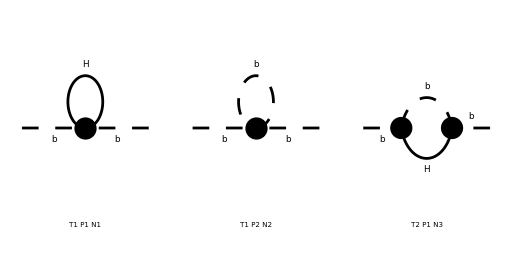

> Top. 1 ac/bc/0.m, 0 diagrams

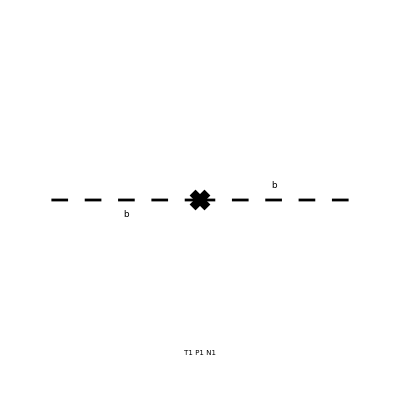

```mathematica
D1Lbb=diag[1,{S[2]},{S[2]}];
```

```mathematica
Amp1Lbb=D1Lbb//amp1L[{p1},{p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 1 Particles amplitude

in total: 3 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ g4^2 vev^2)/(64 π^4 (l^2-(g4 vev^2)/2).(l-p1)^2)-(ⅈ g4)/(64 π^4 (l^2-(g4 vev^2)/2))-(3 ⅈ g4)/(64 π^4 l^2),-ⅈ (ⅈ p1^2 (Zb-1)-1/4 ⅈ g4 vev^2 Zb (Zv-1) (Zv+1))}

```mathematica
Amp1LbbDiv=Amp1Lbb//amp1LSimplify[{Zb:> 1+Nd db,Zv:> 1+Nd dv},{SMP["Delta"],db,dv}]//ExpandAll
```

db p1^2-1/2 dv g4 vev^2+(3 Δ g4^2 vev^2)/(64 π^2)

```mathematica
Amp1LbbDiv//.dvalues
```

db p1^2

```mathematica
dsol[4]=Solve[SelectNotFree2[Amp1LbbDiv,p1]==0,db]//Flatten//Simplify
dSave[dsol[4]];
```

{db→0}

## One Loop (2->1)

## One Loop H->HH

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

in total: 8 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bece/dede.m, 0 diagrams

> Top. 3 ad/becd/eded.m, 0 diagrams

> Top. 4 ad/bdce/eded.m, 0 diagrams

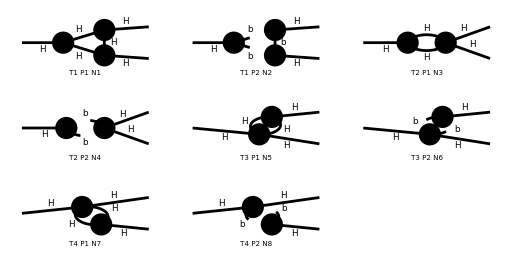

> Top. 1 ad/bdcd/0.m, 0 diagrams

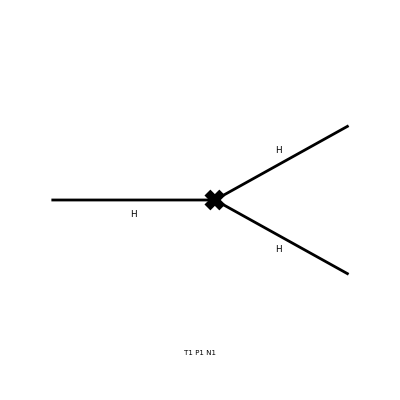

```mathematica
D1LHHH=diag[1,{S[1]},{S[1],S[1]}];
```

```mathematica
Amp1LHHH=D1LHHH//amp1L[{2p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

in total: 8 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(27 ⅈ g4^3 vev^3)/(128 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-(g4 vev^2)/2))-(9 ⅈ g4^2 vev)/(128 π^4 (l^2-(g4 vev^2)/2).((l-2 p1)^2-(g4 vev^2)/2))-(9 ⅈ g4^2 vev)/(64 π^4 (l^2-(g4 vev^2)/2).((l+p1)^2-(g4 vev^2)/2))+-(ⅈ g4^3 vev^3)/(128 π^4 l^2.(l-p1)^2.(l-2 p1)^2)-(ⅈ g4^2 vev)/(128 π^4 l^2.(l-2 p1)^2)-(ⅈ g4^2 vev)/(64 π^4 l^2.(l+p1)^2),-3/2 g4 vev (ZH^(3/2) ZHHH Zv-1)}

```mathematica
Amp1LHHHDiv=Amp1LHHH//amp1LSimplify[{ZHHH:> 1+Nd dHHH,ZH:> 1+Nd dH,Zv:> 1+Nd dv},{SMP["Delta"],dHHH,dH,dv}]//Simplify
```

-(3 g4 vev (8 π^2 (3 dH+2 (dHHH+dv))-5 Δ g4))/(32 π^2)

```mathematica
dsol[5]=Solve[SelectNotFree2[Amp1LHHHDiv/.dSub[dHHH],{SMP["Delta"],dHHH}]==0,dHHH]//Flatten//Simplify
dSave[dsol[5]];
```

{dHHH→(7 Δ g4)/(32 π^2)}

## One Loop H->bb

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 6 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bece/dede.m, 0 diagrams

> Top. 3 ad/becd/eded.m, 0 diagrams

> Top. 4 ad/bdce/eded.m, 0 diagrams

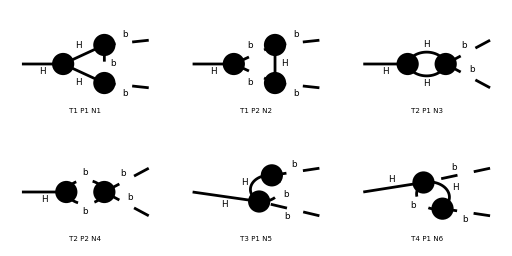

> Top. 1 ad/bdcd/0.m, 0 diagrams

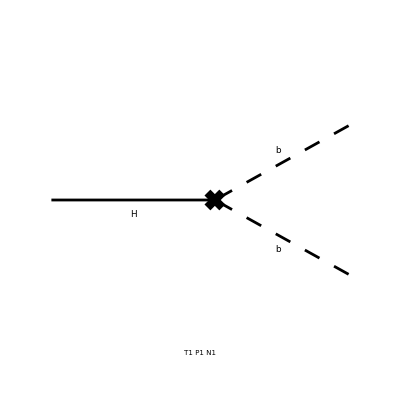

```mathematica
D1LHbb=diag[1,{S[1]},{S[2],S[2]}];
```

```mathematica
Amp1LHbb=D1LHbb//amp1L[{2p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 1 Particles amplitude

> Top. 4: 1 Particles amplitude

in total: 6 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ g4^3 vev^3)/(128 π^4 l^2.((l-p1)^2-(g4 vev^2)/2).(l-2 p1)^2)-(3 ⅈ g4^3 vev^3)/(128 π^4 (l^2-(g4 vev^2)/2).(l-p1)^2.((l-2 p1)^2-(g4 vev^2)/2))-(3 ⅈ g4^2 vev)/(128 π^4 (l^2-(g4 vev^2)/2).((l-2 p1)^2-(g4 vev^2)/2))-(ⅈ g4^2 vev)/(32 π^4 (l^2-(g4 vev^2)/2).(l+p1)^2)-(3 ⅈ g4^2 vev)/(128 π^4 l^2.(l-2 p1)^2),-1/2 g4 vev (Zb ZbbH √ZH Zv-1)}

```mathematica
Amp1LHbbDiv=Amp1LHbb//amp1LSimplify[{ZbbH:> 1+Nd dbbH,Zb:> 1+Nd db,ZH:> 1+Nd dH,Zv:> 1+Nd dv},{SMP["Delta"],dbbH,db,dH,dv}]//Simplify
```

(g4 vev (5 Δ g4-8 π^2 (2 db+2 dbbH+dH+2 dv)))/(32 π^2)

```mathematica
dsol[6]=Solve[SelectNotFree2[Amp1LHbbDiv/.dSub[dbbH],{SMP["Delta"],dbbH}]==0,dbbH]//Flatten//Simplify
dSave[dsol[6]];
```

{dbbH→(7 Δ g4)/(32 π^2)}

## One Loop (2->2)

## One Loop HH->HH

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

> Top. 5: 2 Particles insertions

> Top. 6: 2 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 2 Particles insertions

> Top. 9: 2 Particles insertions

> Top. 10: 2 Particles insertions

> Top. 11: 2 Particles insertions

> Top. 12: 2 Particles insertions

in total: 24 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

> Top. 2 aebf/cgdf/egefgf.m, 0 diagrams

> Top. 3 aebf/cfdg/egefgf.m, 0 diagrams

> Top. 4 aebf/cgde/fgfege.m, 0 diagrams

> Top. 5 aebf/cedg/fgfege.m, 0 diagrams

> Top. 6 aebe/cfdg/fgfege.m, 0 diagrams

> Top. 7 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 8 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 9 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 10 aebe/cfdf/efef.m, 0 diagrams

> Top. 11 aebf/cedf/efef.m, 0 diagrams

> Top. 12 aebf/cfde/efef.m, 0 diagrams

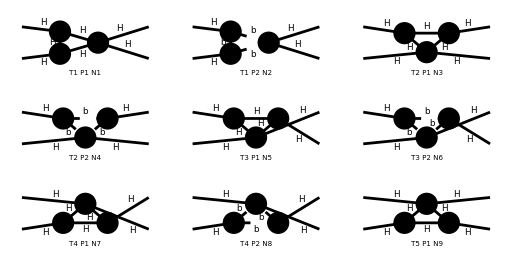

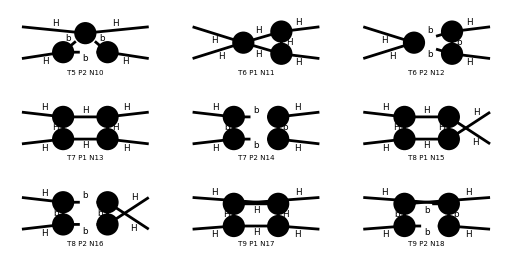

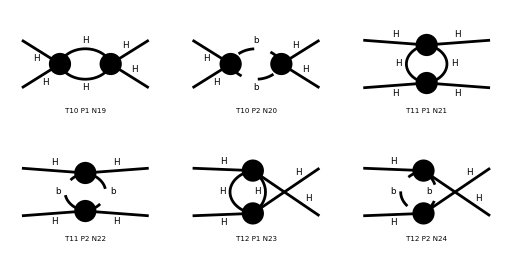

> Top. 1 aebe/cede/0.m, 0 diagrams

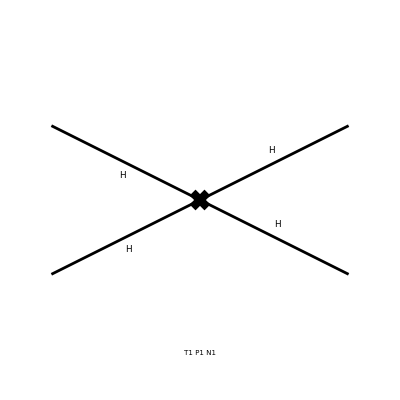

```mathematica
D1LHHHH=diag[1,{S[1],S[1]},{S[1],S[1]}];
```

```mathematica
Amp1LHHHH=D1LHHHH//amp1L[{p1,p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

> Top. 5: 2 Particles amplitudes

> Top. 6: 2 Particles amplitudes

> Top. 7: 2 Particles amplitudes

> Top. 8: 2 Particles amplitudes

> Top. 9: 2 Particles amplitudes

> Top. 10: 2 Particles amplitudes

> Top. 11: 2 Particles amplitudes

> Top. 12: 2 Particles amplitudes

in total: 24 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(81 ⅈ g4^4 vev^4)/(256 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2-(g4 vev^2)/2).(l^2-(g4 vev^2)/2).((l-p1)^2-(g4 vev^2)/2))-(81 ⅈ g4^4 vev^4)/(128 π^4 (l^2-(g4 vev^2)/2).((l+p1)^2-(g4 vev^2)/2).(l^2-(g4 vev^2)/2).((l-p1)^2-(g4 vev^2)/2))-(27 ⅈ g4^3 vev^2)/(32 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2-(g4 vev^2)/2)^2)-(27 ⅈ g4^3 vev^2)/(64 π^4 (l^2-(g4 vev^2)/2).((l+p1)^2-(g4 vev^2)/2).((l-p1)^2-(g4 vev^2)/2))-(9 ⅈ g4^2)/(128 π^4 (l^2-(g4 vev^2)/2).((l-2 p1)^2-(g4 vev^2)/2))-(9 ⅈ g4^2)/(64 π^4 (l^2-(g4 vev^2)/2)^2)+-(ⅈ g4^4 vev^4)/(256 π^4 l^2.(l-p1)^2.l^2.(l-p1)^2)-(ⅈ g4^4 vev^4)/(128 π^4 l^2.(l+p1)^2.l^2.(l-p1)^2)-(ⅈ g4^3 vev^2)/(32 π^4 l^2.((l-p1)^2)^2)-(ⅈ g4^3 vev^2)/(64 π^4 l^2.(l+p1)^2.(l-p1)^2)-(ⅈ g4^2)/(128 π^4 l^2.(l-2 p1)^2)-(ⅈ g4^2)/(64 π^4 (l^2)^2),-3/2 g4 (ZH^2 ZHHHH-1)}

```mathematica
Amp1LHHHHDiv=Amp1LHHHH//amp1LSimplify[{ZHHHH:> 1+Nd dHHHH,ZH:> 1+Nd dH},{SMP["Delta"],dHHHH,dH}]//Simplify
```

3/32 g4 ((5 Δ g4)/π^2-16 (2 dH+dHHHH))

```mathematica
dsol[7]=Solve[SelectNotFree2[Amp1LHHHHDiv/.dSub[dHHHH],{SMP["Delta"],dHHHH}]==0,dHHHH]//Flatten//Simplify
dSave[dsol[7]];
```

{dHHHH→(5 Δ g4)/(16 π^2)}

## One Loop Hb->Hb

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

> Top. 5: 2 Particles insertions

> Top. 6: 2 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 2 Particles insertions

> Top. 9: 2 Particles insertions

> Top. 10: 2 Particles insertions

> Top. 11: 2 Particles insertions

> Top. 12: 2 Particles insertions

in total: 24 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

> Top. 2 aebf/cgdf/egefgf.m, 0 diagrams

> Top. 3 aebf/cfdg/egefgf.m, 0 diagrams

> Top. 4 aebf/cgde/fgfege.m, 0 diagrams

> Top. 5 aebf/cedg/fgfege.m, 0 diagrams

> Top. 6 aebe/cfdg/fgfege.m, 0 diagrams

> Top. 7 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 8 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 9 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 10 aebe/cfdf/efef.m, 0 diagrams

> Top. 11 aebf/cedf/efef.m, 0 diagrams

> Top. 12 aebf/cfde/efef.m, 0 diagrams

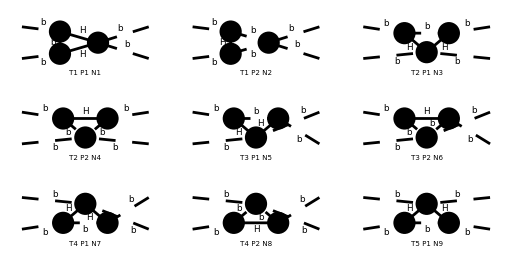

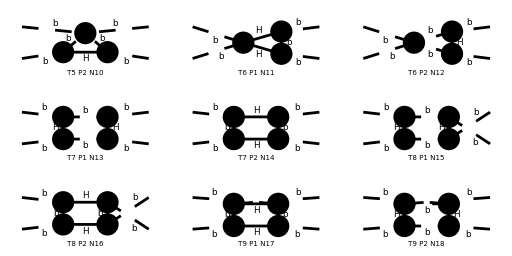

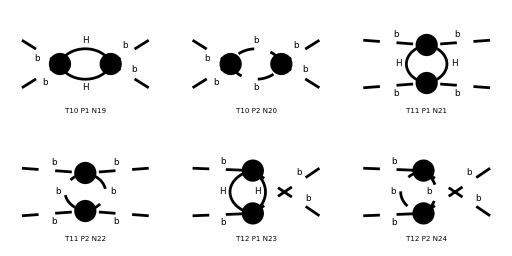

> Top. 1 aebe/cede/0.m, 0 diagrams

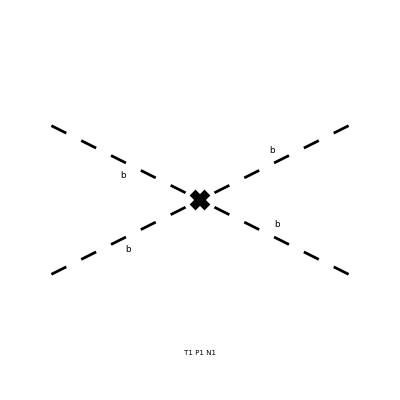

```mathematica
D1Lbbbb=diag[1,{S[2],S[2]},{S[2],S[2]}];
```

```mathematica
Amp1Lbbbb=D1Lbbbb//amp1L[{p1,p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

> Top. 5: 2 Particles amplitudes

> Top. 6: 2 Particles amplitudes

> Top. 7: 2 Particles amplitudes

> Top. 8: 2 Particles amplitudes

> Top. 9: 2 Particles amplitudes

> Top. 10: 2 Particles amplitudes

> Top. 11: 2 Particles amplitudes

> Top. 12: 2 Particles amplitudes

in total: 24 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ g4^4 vev^4)/(256 π^4 l^2.((l-p1)^2-(g4 vev^2)/2).l^2.((l-p1)^2-(g4 vev^2)/2))-(ⅈ g4^4 vev^4)/(128 π^4 l^2.((l+p1)^2-(g4 vev^2)/2).l^2.((l-p1)^2-(g4 vev^2)/2))-(ⅈ g4^4 vev^4)/(256 π^4 (l^2-(g4 vev^2)/2).(l-p1)^2.(l^2-(g4 vev^2)/2).(l-p1)^2)-(ⅈ g4^4 vev^4)/(128 π^4 (l^2-(g4 vev^2)/2).(l+p1)^2.(l^2-(g4 vev^2)/2).(l-p1)^2)-(ⅈ g4^3 vev^2)/(32 π^4 l^2.((l-p1)^2-(g4 vev^2)/2)^2)-(ⅈ g4^3 vev^2)/(64 π^4 l^2.((l+p1)^2-(g4 vev^2)/2).((l-p1)^2-(g4 vev^2)/2))-(3 ⅈ g4^3 vev^2)/(32 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2)^2)-(3 ⅈ g4^3 vev^2)/(64 π^4 (l^2-(g4 vev^2)/2).(l+p1)^2.(l-p1)^2)-(ⅈ g4^2)/(128 π^4 (l^2-(g4 vev^2)/2).((l-2 p1)^2-(g4 vev^2)/2))-(ⅈ g4^2)/(64 π^4 (l^2-(g4 vev^2)/2)^2)-(9 ⅈ g4^2)/(128 π^4 l^2.(l-2 p1)^2)-(9 ⅈ g4^2)/(64 π^4 (l^2)^2),-3/2 g4 (Zb^2 Zbbbb-1)}

```mathematica
Amp1LbbbbDiv=Amp1Lbbbb//amp1LSimplify[{Zbbbb:> 1+Nd dbbbb,Zb:> 1+Nd db},{SMP["Delta"],dbbbb,db}]//Simplify
```

3/32 g4 ((5 Δ g4)/π^2-16 (2 db+dbbbb))

```mathematica
dsol[8]=Solve[SelectNotFree2[Amp1LbbbbDiv/.dSub[dbbbb],{SMP["Delta"],dbbbb}]==0,dbbbb]//Flatten//Simplify
dSave[dsol[8]];
```

{dbbbb→(5 Δ g4)/(16 π^2)}

## One Loop Hb->Hb

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

> Top. 5: 2 Particles insertions

> Top. 6: 2 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 2 Particles insertions

> Top. 9: 2 Particles insertions

> Top. 10: 1 Particles insertion

> Top. 11: 2 Particles insertions

> Top. 12: 1 Particles insertion

in total: 22 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

> Top. 2 aebf/cgdf/egefgf.m, 0 diagrams

> Top. 3 aebf/cfdg/egefgf.m, 0 diagrams

> Top. 4 aebf/cgde/fgfege.m, 0 diagrams

> Top. 5 aebf/cedg/fgfege.m, 0 diagrams

> Top. 6 aebe/cfdg/fgfege.m, 0 diagrams

> Top. 7 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 8 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 9 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 10 aebe/cfdf/efef.m, 0 diagrams

> Top. 11 aebf/cedf/efef.m, 0 diagrams

> Top. 12 aebf/cfde/efef.m, 0 diagrams

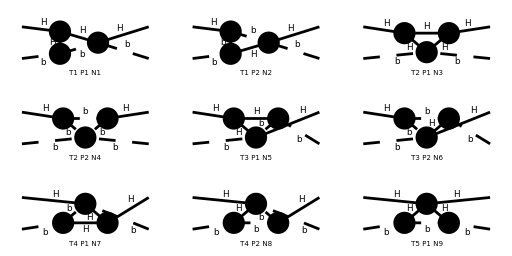

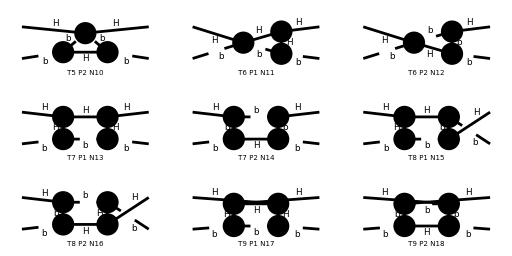

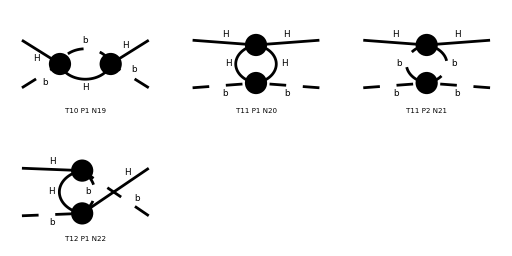

> Top. 1 aebe/cede/0.m, 0 diagrams

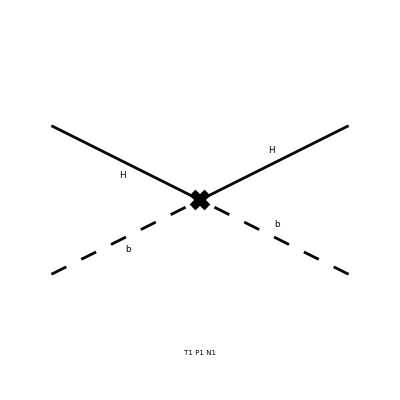

```mathematica
D1LHbHb=diag[1,{S[1],S[2]},{S[1],S[2]}];
```

```mathematica
Amp1LHbHb=D1LHbHb//amp1L[{p1,p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

> Top. 5: 2 Particles amplitudes

> Top. 6: 2 Particles amplitudes

> Top. 7: 2 Particles amplitudes

> Top. 8: 2 Particles amplitudes

> Top. 9: 2 Particles amplitudes

> Top. 10: 1 Particles amplitude

> Top. 11: 2 Particles amplitudes

> Top. 12: 1 Particles amplitude

in total: 22 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ g4^4 vev^4)/(256 π^4 l^2.(l-p1)^2.(l^2-(g4 vev^2)/2).(l-p1)^2)-(ⅈ g4^4 vev^4)/(256 π^4 l^2.((l+p1)^2-(g4 vev^2)/2).l^2.(l-p1)^2)-(3 ⅈ g4^4 vev^4)/(256 π^4 l^2.((l+p1)^2-(g4 vev^2)/2).(l^2-(g4 vev^2)/2).(l-p1)^2)-(9 ⅈ g4^4 vev^4)/(256 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2-(g4 vev^2)/2).l^2.((l-p1)^2-(g4 vev^2)/2))-(3 ⅈ g4^4 vev^4)/(256 π^4 (l^2-(g4 vev^2)/2).(l+p1)^2.l^2.((l-p1)^2-(g4 vev^2)/2))-(9 ⅈ g4^4 vev^4)/(256 π^4 (l^2-(g4 vev^2)/2).(l+p1)^2.(l^2-(g4 vev^2)/2).((l-p1)^2-(g4 vev^2)/2))-(3 ⅈ g4^3 vev^2)/(128 π^4 l^2.((l-p1)^2)^2)-(ⅈ g4^3 vev^2)/(64 π^4 l^2.((l-p1)^2-(g4 vev^2)/2).(l-p1)^2)-(3 ⅈ g4^3 vev^2)/(128 π^4 l^2.((l-p1)^2-(g4 vev^2)/2)^2)-(ⅈ g4^3 vev^2)/(128 π^4 l^2.(l+p1)^2.((l-p1)^2-(g4 vev^2)/2))-(ⅈ g4^3 vev^2)/(128 π^4 l^2.((l+p1)^2-(g4 vev^2)/2).(l-p1)^2)-(ⅈ g4^3 vev^2)/(128 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2)^2)-(3 ⅈ g4^3 vev^2)/(64 π^4 (l^2-(g4 vev^2)/2).(l-p1)^2.((l-p1)^2-(g4 vev^2)/2))-(9 ⅈ g4^3 vev^2)/(128 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2-(g4 vev^2)/2)^2)-(3 ⅈ g4^3 vev^2)/(128 π^4 (l^2-(g4 vev^2)/2).(l+p1)^2.((l-p1)^2-(g4 vev^2)/2))-(3 ⅈ g4^3 vev^2)/(128 π^4 (l^2-(g4 vev^2)/2).((l+p1)^2-(g4 vev^2)/2).(l-p1)^2)-(3 ⅈ g4^2)/(128 π^4 (l^2)^2)-(ⅈ g4^2)/(64 π^4 (l^2-(g4 vev^2)/2).l^2)-(3 ⅈ g4^2)/(128 π^4 (l^2-(g4 vev^2)/2)^2)-(ⅈ g4^2)/(64 π^4 (l^2-(g4 vev^2)/2).(l-2 p1)^2),-1/2 g4 (Zb ZbbHH ZH-1)}

```mathematica
Amp1LHbHbDiv=Amp1LHbHb//amp1LSimplify[{ZbbHH:> 1+Nd dbbHH,ZH:> 1+Nd dH,Zb:> 1+Nd db},{SMP["Delta"],dbbHH,dH,db}]//Simplify
```

1/32 g4 ((5 Δ g4)/π^2-16 (db+dbbHH+dH))

```mathematica
dsol[9]=Solve[SelectNotFree2[Amp1LHbHbDiv/.dSub[dbbHH],{SMP["Delta"],dbbHH}]==0,dbbHH]//Flatten//Simplify
dSave[dsol[9]];
```

{dbbHH→(5 Δ g4)/(16 π^2)}

## Final answers

```mathematica
dvalues
```

{dv→(3 Δ g4)/(32 π^2),dH→0,dmH→(Δ g4)/(16 π^2),db→0,dHHH→(7 Δ g4)/(32 π^2),dbbH→(7 Δ g4)/(32 π^2),dHHHH→(5 Δ g4)/(16 π^2),dbbbb→(5 Δ g4)/(16 π^2),dbbHH→(5 Δ g4)/(16 π^2)}

```mathematica
M$IntParams
```

{mb→0,mH→(√g4 vev)/(√2)}